```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
```

```mathematica
(*Example in paper*)
fp1={-2.2,0.1}; fp2={1.15,0.38};
li=1.23773;lc=3.5721;lo=4.6712;
cp={-.8253,-1.0329}; cAng=91.91°;

mp1Rel={1.24,.1,1};
Rot={{Cos[cAng],-Sin[cAng],cp[[1]]},{Sin[cAng],Cos[cAng],cp[[2]]},{0,0,1}};
mp1=(Rot.mp1Rel)[[1;;2]]
initAng=ArcTan[mp1⟦1⟧-fp1⟦1⟧,mp1⟦2⟧-fp1⟦2⟧];
npathpoints=20;
```

{-0.966573,0.203078}

```mathematica
(*Sample Example*)
(*fp1={0,0}; fp2={4,0};
mp1={1,0};mp2={3,3};
cp={0,3};cAng=90°;
npathpoints=50;

li=Norm[fp1-mp1];lo=Norm[fp2-mp2];lc=Norm[mp1-mp2];
initAng=ArcTan[mp1⟦1⟧-fp1⟦1⟧,mp1⟦2⟧-fp1⟦2⟧];*)
```

```mathematica
(*Calculating required parameters*)
pose={};
(*Calc Cplr link param*)
A=mp1;B=fp2;r2=lo;r1=lc;
dist=Norm[A-B];
cosAlpha=(r1^2+dist^2-r2^2)/(2r1 dist);
uAB=(B-A)/dist;
puAB={uAB⟦2⟧,-uAB⟦1⟧};
intersect1=A+uAB*(r1*cosAlpha)+puAB*(r1*Sqrt[1-cosAlpha^2]);
intersect2=A+uAB*(r1*cosAlpha)-puAB*(r1*Sqrt[1-cosAlpha^2]);
mp2=intersect2;

angMp1Cp=ArcTan[cp⟦1⟧-mp1⟦1⟧,cp⟦2⟧-mp1⟦2⟧];
angMp1Mp2=ArcTan[mp2⟦1⟧-mp1⟦1⟧,mp2⟦2⟧-mp1⟦2⟧];
angCp1=angMp1Cp-angMp1Mp2;
lCp1=Norm[mp1-cp];
angCpDelta=cAng-angMp1Cp;
Print["Mp2=",mp2]
Print["Cplr len=",lCp1,", Cplr ang=",angCp1/Degree,", Pose delta",angCpDelta/Degree]
```

Mp2={-2.3176,3.50983}

Cplr len=1.24403, Cplr ang=-195.703, Pose delta175.389

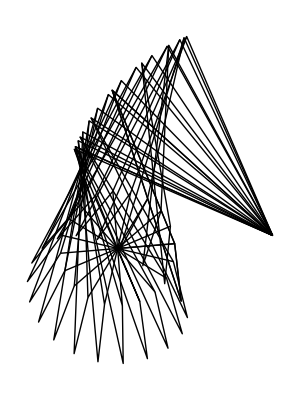

```mathematica
(*Simulating the Four-bar*)
mech={};
OutPos={};
OutAng={};
For[i=0,i<=2 Pi,i+=2Pi/npathpoints,
mp1i=fp1+li{Cos[i+initAng],Sin[i+initAng]};

(*Circle-Circle intersection*)
A=mp1i;B=fp2;r2=lo;r1=lc;
dist=Norm[A-B];
cosAlpha=(r1^2+dist^2-r2^2)/(2r1 dist);
uAB=(B-A)/dist;
puAB={uAB⟦2⟧,-uAB⟦1⟧};
intersect1=A+uAB*(r1*cosAlpha)+puAB*(r1*Sqrt[1-cosAlpha^2]);
intersect2=A+uAB*(r1*cosAlpha)-puAB*(r1*Sqrt[1-cosAlpha^2]);
mp2i=intersect2;

angMp1Mp2i=ArcTan[mp2i⟦1⟧-mp1i⟦1⟧,mp2i⟦2⟧-mp1i⟦2⟧];
cpi=mp1i+lCp1{Cos[angMp1Mp2i+angCp1],Sin[angMp1Mp2i+angCp1]};
cAngi=angCpDelta+angMp1Mp2i+angCp1;
(*Print[N[cpi],N[cAngi]/Degree];*)
OutPos=Append[OutPos,cpi];
OutAng=Append[OutAng,cAngi];
mech=Append[mech,Line[{fp1,mp1i,mp2i,fp2}]];
mech=Append[mech,Line[{mp1i,cpi,mp2i}]];
]
Graphics[mech]
```

```mathematica
MatrixForm[Transpose[N[Join[OutPos,Transpose[{OutAng/Degree}],2]]]]
N[Transpose[OutPos]];
N[OutAng]/Degree;
```

(-0.825295 | -1.18239 | -1.65538 | -2.15301 | -2.63917 | -3.0963 | -3.50276 | -3.8315 | -4.0549 | -4.14993 | -4.10224 | -3.909 | -3.58056 | -3.14061 | -2.625 | -2.07931 | -1.55571 | -1.1102 | -0.80153 | -0.690762 | -0.825295
-1.0329 | -0.658686 | -0.272048 | 0.0657309 | 0.292049 | 0.375097 | 0.308835 | 0.104498 | -0.214052 | -0.613148 | -1.05203 | -1.48608 | -1.87075 | -2.16601 | -2.34082 | -2.37733 | -2.27423 | -2.04906 | -1.73826 | -1.38935 | -1.0329
91.9101 | 79.6875 | 66.9903 | 56.8365 | 49.8961 | 45.7746 | 43.9348 | 43.9631 | 45.5812 | 48.5998 | 52.8679 | 58.2333 | 64.5146 | 71.482 | 78.8404 | 86.2004 | 93.0159 | 98.4634 | 101.251 | 99.5492 | 91.9101)